```mathematica
SetDirectory["/home/student/compphys/week6"]
```

/home/student/compphys/week6

```mathematica
data=Partition[ReadList["!./chisq 10",Number],3]
```

{{1.,5.5,0.5},{2.,16.501,0.5},{3.,33.5416,0.5},{4.,56.6766,0.5},{5.,85.8646,0.5},{6.,120.591,0.5},{7.,161.592,0.5},{8.,208.987,0.5},{9.,262.027,0.5},{10.,320.954,0.5},{0.459749,2.03146,3.00236}}

```mathematica
Needs["ErrorBarPlots`"]
```

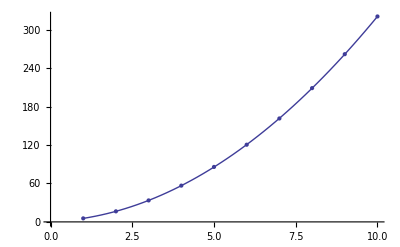

```mathematica
Show[ErrorListPlot[Table[{{data[[i,1]],data[[i,2]]},ErrorBar[data[[i,3]]]},{i,10}]],Plot[data[[11,1]]+data[[11,2]]x+data[[11,3]]x^2,{x,1,10}]]
```

```mathematica
data=Partition[ReadList["!./chisq 10 100000",Number],4];
```

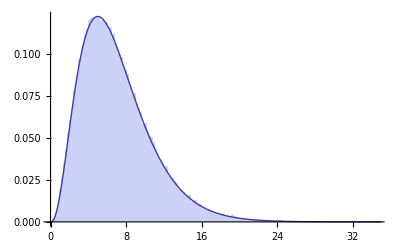

```mathematica
Show[Histogram[data[[All,4]],100,"PDF"],Plot[PDF[ChiSquareDistribution[7],x],{x,0,35}]]
```

```mathematica
1-CDF[ChiSquareDistribution[7],3.]
```

0.885002